```mathematica
data=SemanticImport["D:\\Google Drive\\Rich Internship 2020\\XGBoost\\xgboost_covid\\data\\X_data removed missing values.csv"];
```

```mathematica
ProgressIndicator[Dynamic[i],{3,77}]
```

```mathematica
data2=Table[Values[Transpose[Normal[SynthesizeMissingValues[Normal[data[All,{2,i}]],Method-><|"LearningMethod"->"KernelDensityEstimation", "EvaluationStrategy"->"ModeFinding"|>,PerformanceGoal->"Quality"]]]⟦2⟧],{i,3,77}];
Export["processed data by age.csv",Transpose[data2]]
```

processed data by age.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["processed data by age.csv"]]]
```

```mathematica
ld=LearnDistribution[Normal[data[All,{2,75}]],Method->"KernelDensityEstimation"]
```

LearnedDistribution[…]

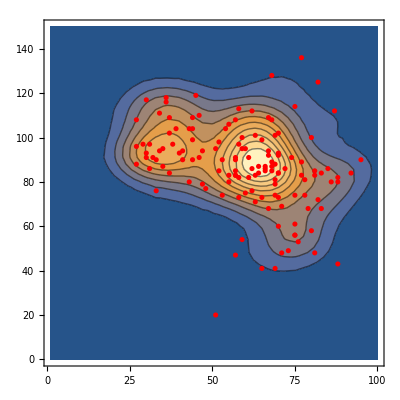

```mathematica
Show[ContourPlot[PDF[ld,{x,y}],{x,1,100},{y,0,150},PlotRange->All,Contours->10],ListPlot[Normal[data[All,{2,75}]], PlotStyle->Red]]
```

```mathematica
ProgressIndicator[Dynamic[i],{4,77}]
```

```mathematica
data3=Table[Values[Transpose[Normal[SynthesizeMissingValues[Normal[data[All,{2,3,i}]],Method-><|"LearningMethod"->"KernelDensityEstimation", "EvaluationStrategy"->"ModeFinding"|>,PerformanceGoal->"Quality"]]]⟦3⟧],{i,4,77}];
```

```mathematica
Export["processed data by age and gender.csv",Transpose[data3]]
```

processed data by age and gender.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["processed data by age and gender.csv"]]]
```